## UniversalQComplier Examples File

### Basic Gate types

This package decomposes arbitrary gates into a sequence of CNOTs and single qubit rotations. The latter are expressed using the convention that an rotation by angle t about the x-axis of the Bloch sphere is

```mathematica
RxM[t,1]//MatrixForm
```

(Cos[t/2] | ⅈ Sin[t/2]
ⅈ Sin[t/2] | Cos[t/2])

A y-rotation by angle t is:

```mathematica
RyM[t,1]//MatrixForm
```

(Cos[t/2] | Sin[t/2]
-Sin[t/2] | Cos[t/2])

And a z-rotation is

```mathematica
RzM[t,1]//MatrixForm
```

(ⅇ^((ⅈ t)/2) | 0
0 | ⅇ^(-(ⅈ t)/2))

A CNOT with qubit 1 as the control and 2 as the target is

```mathematica
CNOTM[1,2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

#### Single-qubit unitaries

Choose a random 2x2 unitary and decompose it into a Z rotation, a Y rotation then a Z rotation

```mathematica
u=PickRandomUnitary[2]
```

{{-0.35917-0.548312 ⅈ,0.536212-0.531815 ⅈ},{-0.184883+0.732235 ⅈ,0.654784+0.0301123 ⅈ}}

```mathematica
gates=ZYZDec[u]
```

{{3,4.91376,1},{2,1.71197,1},{3,5.45595,1}}

This is the standard form for gate outputs. The first gate in the list is an Rz on qubit 1, etc.  We can construct the unitary from these (up to phase) as follows. To get a reminder of the conventions, use GateTypes[]

```mathematica
GateTypes[]
```

Gate types for UniversalQCompiler

{-2,diag,act}: diagonal gate with entries diag on the qubits listed in act

{-1,n,m}: CZ with qubit n the control and m the target

{0,n,m}: CNOT with qubit n the control and m the target

{1,t,n}: x-rotation by angle t for qubit n

{2,t,n}: y-rotation by angle t for qubit n

{3,t,n}: z-rotation by angle t for qubit n

{4,0,n}: trace out qubit n

{4,1,n}: measure qubit n in the computational basis

{5,0,n}: qubit n starts in state |0>

{5,1,n}: qubit n starts in state |1>

{6,0,n}: qubit n is postselected on |0>

{6,1,n}: qubit n is postselected on |1>

{-10,t,{n,m}}: XX-gate with angle t on qubits n,m

{-11,{t,p},n}: R-gate with angles t,p on qubit n

Confirm the result (note that decompositions are always up to phase)

```mathematica
outu=CreateOperationFromGateList[gates]
```

{{0.298295-0.583669 ⅈ,0.727634+0.202237 ⅈ},{-0.727634+0.202237 ⅈ,0.298295+0.583669 ⅈ}}

This is equal to u up to phase:

```mathematica
Chop[outu/outu[[1,1]]*u[[1,1]]-u]
```

{{0,0},{0,0}}

We get the same result from the Quantum Shannon Decomposition

```mathematica
gatelist=QSD[u]
```

{{3,4.91376,1},{2,1.71197,1},{3,5.45595,1}}

We can also re-express the output in string form

```mathematica
ListFormToStr[gatelist]
```

{Rz(4.91376)(1),Ry(1.71197)(1),Rz(5.45595)(1)}

Or as matrices

```mathematica
Map[MatrixForm,ListFormToOp[gatelist]]
```

{(-0.774599+0.632452 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.774599-0.632452 ⅈ),(0.655477+0. ⅈ | 0.755216+0. ⅈ
-0.755216+0. ⅈ | 0.655477+0. ⅈ),(-0.915672+0.401926 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.915672-0.401926 ⅈ)}

Or draw the topology for it:

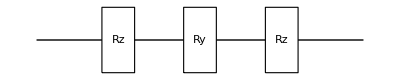

```mathematica
PrintCircuit[gatelist]
```

If you use the package QCircuit in LATEX then the command LatexQCircuit can be used to generate the circuit in a compatible form:

```mathematica
LatexQCircuit[gatelist]
```

{
& \qw  & \gate{R_z} & \gate{R_y} & \gate{R_z} & \qw  
}

Using the option AnglePrecision→2 gives the angles to two significant figures.

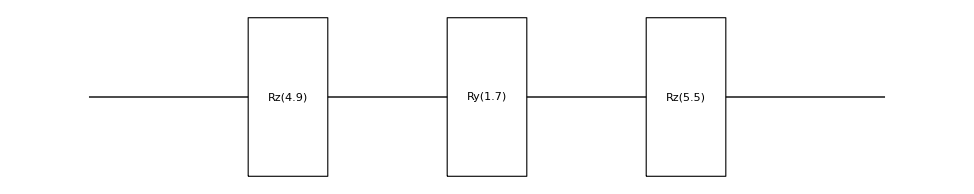

```mathematica
PrintCircuit[gatelist,AnglePrecision->2]
```

```mathematica
LatexQCircuit[gatelist,AnglePrecision->2]
```

{
& \qw  & \gate{R_z(\textnormal{$4.9$})} & \gate{R_y(\textnormal{$1.7$})} & \gate{R_z(\textnormal{$5.5$})} & \qw  
}

### Two qubit unitaries

#### Using QSD

Now choose a real two-qubit gate and do the Quantum Shannon Decomposition. The decomposition achieves the minimal number of required CNOT gates for arbitrary (and not necessarily generic) two qubit gates (and is equivalent to calling DecUnitary2Qubits in the considered case).

```mathematica
u=RPickRandomUnitary[4];u//MatrixForm
```

(0.27403 | 0.60353 | 0.0491122 | 0.747159
-0.431234 | -0.223208 | 0.826736 | 0.284118
0.854943 | -0.229555 | 0.437897 | -0.156918
-0.0895389 | 0.730229 | 0.349774 | -0.580006)

```mathematica
gatelist=QSD[u]
```

{{3,4.71239,2},{2,1.5708,2},{3,3.04245,2},{3,3.14159,1},{2,2.0275,1},{3,1.5708,1},{0,2,1},{3,5.63206,1},{1,6.02488,1},{1,5.12899,2},{3,3.18062,2},{0,2,1},{2,1.5708,1},{1,1.5708,1},{2,1.5708,2},{3,1.5708,2},{0,1,2},{3,6.28319,2}}

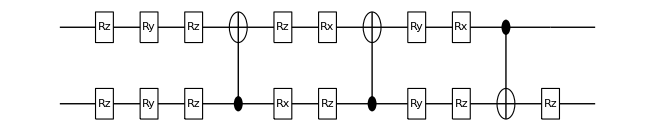

```mathematica
PrintCircuit[gatelist]
```

```mathematica
LatexQCircuit[gatelist]
```

{
& \qw  & \gate{R_z} & \gate{R_y} & \gate{R_z} & \targ & \gate{R_z} & \gate{R_x} & \targ & \gate{R_y} & \gate{R_x} & \ctrl{1} & \qw  & \qw  \\
& \qw  & \gate{R_z} & \gate{R_y} & \gate{R_z} & \ctrl{-1} & \gate{R_x} & \gate{R_z} & \ctrl{-1} & \gate{R_y} & \gate{R_z} & \targ & \gate{R_z} & \qw  
}

We can check the result as before:

```mathematica
outu=CreateOperationFromGateList[gatelist];Chop[outu/outu[[1,1]]*u[[1,1]]-u]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

We can also apply u to other qubits using the second argument of QSD to specify. E.g. to the second and fourth qubits

```mathematica
gatelist=QSD[u,{2,4}]
```

{{3,4.71239,4},{2,1.5708,4},{3,3.04245,4},{3,3.14159,2},{2,2.0275,2},{3,1.5708,2},{0,4,2},{3,5.63206,2},{1,6.02488,2},{1,5.12899,4},{3,3.18062,4},{0,4,2},{2,1.5708,2},{1,1.5708,2},{2,1.5708,4},{3,1.5708,4},{0,2,4},{3,6.28319,4}}

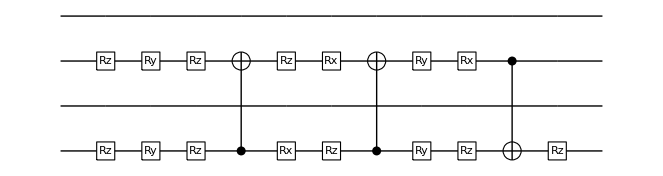

```mathematica
PrintCircuit[gatelist]
```

Or, reversing the gates to the fourth and second qubits

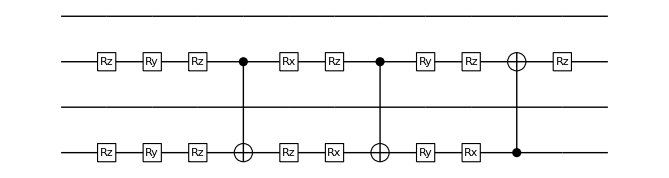

```mathematica
PrintCircuit[QSD[u,{4,2}]]
```

#### Using the Knill decomposition

We could also use another decomposition

```mathematica
gatelist=KnillDec[u]
```

{{3,2.72275,2},{2,1.39891,2},{3,4.93724,2},{3,4.66606,1},{2,1.25649,1},{0,1,2},{3,0.808228,2},{2,5.43269,1},{0,2,1},{3,0.808228,1},{1,3.79927,1},{0,2,1},{2,1.92131,1},{1,0.985066,1},{1,0.326915,2},{0,1,2},{2,2.26783,2},{1,3.46851,2},{2,2.50641,1},{3,0.148848,1},{0,1,2},{3,5.47496,2},{2,5.43269,1},{0,2,1},{3,5.47496,1},{1,1.13288,1},{0,2,1},{2,0.592119,1},{1,5.9075,1},{1,0.726477,2},{0,1,2},{2,1.3438,2},{1,1.19423,2},{2,1.62684,1},{3,5.02516,1},{0,1,2},{3,π/2,2},{2,6.07835,1},{0,2,1},{3,π/2,1},{1,4.50756,1},{0,2,1},{2,1.5708,1},{1,1.5708,1},{0,1,2},{2,2.67752,2},{3,3.14159,2},{2,1.89263,1}}

In this case, the output is much longer, but still gives the same result

```mathematica
CNOTCount[gatelist]
```

12

```mathematica
outu=CreateOperationFromGateList[gatelist];Chop[outu/outu[[1,1]]*u[[1,1]]-u]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

#### Using the column by column decomposition

The other decomposition we can do is the column-by-column decomposition

```mathematica
gatelist=ColumnByColumnDec[u]
```

{{3,4.71239,2},{3,5.49779,1},{0,2,1},{3,4.71239,1},{0,2,1},{3,5.49779,1},{2,1.66994,2},{3,3.14159,2},{0,1,2},{2,1.66994,2},{2,2.72499,1},{3,3.14159,1},{0,2,1},{2,2.72499,1},{2,5.42185,2},{0,1,2},{3,3.14159,2},{2,4.75141,2},{2,4.21414,1},{0,1,2},{2,2.67986,2}}

```mathematica
CNOTCount[gatelist]
```

6

```mathematica
outu=CreateOperationFromGateList[gatelist];Chop[outu/outu[[1,1]]*u[[1,1]]-u]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### Decomposition of isometries from m to n qubits

We provide different methods to decompose arbitrary isometries from m to n qubits. Recall that an isometry from m to n qubits corresponds to a unitary operation on n qubits where n-m qubits start in a fixed state |0>.

The method DecIsometry choses automatically the method that achieves the lowest CNOT count. Let’s consider how to decompose a random isometry from one qubit to three qubits.

```mathematica
u=RPickRandomIsometry[2^1,2^3];
```

```mathematica
gatelist=DecIsometry[u]
```

{{5,0,2},{5,0,1},{3,1.1781,2},{2,2.61503,2},{3,3.14159,2},{3,1.76715,1},{2,1.93843,1},{3,3.14159,1},{0,3,1},{2,1.93843,1},{0,1,2},{2,2.1507,2},{0,3,2},{2,0.46433,2},{2,2.17981,3},{3,3.14159,3},{0,2,3},{2,0.738974,3},{1,3.14159,3},{0,1,3},{2,1.03264,3},{1,3.14159,3},{2,0.373714,1},{3,3.14159,1},{0,2,3},{2,2.47347,3},{2,4.13874,2},{3,1.5708,2},{0,1,3},{2,0.228884,3},{1,1.5708,3},{2,1.36434,1},{3,π,1},{0,3,2},{3,0.536817,2},{2,1.50899,3},{3,1.78871,3},{0,3,2},{3,1.5708,2},{2,5.25591,2},{2,1.5708,3},{3,4.71239,3}}

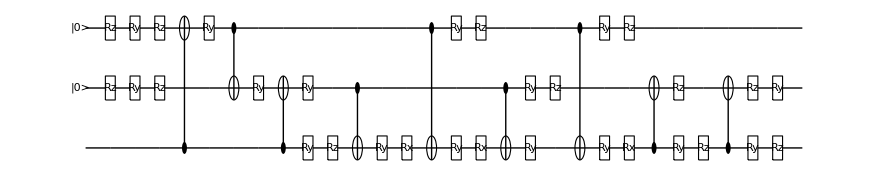

```mathematica
PrintCircuit[gatelist]
```

When multiplying together the gates in a decomposition of an isometry from m to n qubits, the first 2^m columns match the isometry up to phase.  For example, in an isometry from 1 qubit to 3, the first two columns match

```mathematica
outu=IdentityMatrix[2^3];gatelist2=DeleteCases[gatelist,{5,_,_}];For[i=1,i≤Length[gatelist2],i++,outu=ListFormToOp[gatelist2[[i]],3].outu];Chop[outu/outu[[1,1]]*u[[1,1]]]//MatrixForm
```

(0.714526 | -0.425474 | -0.0331768+0.080096 ⅈ | 0.120597-0.291147 ⅈ | -0.0222144-0.111679 ⅈ | 0.00226252+0.0113745 ⅈ | -0.0475285-0.00945401 ⅈ | 0.42316+0.0841718 ⅈ
0.224018 | 0.311936 | -0.019677+0.0475045 ⅈ | 0.16513-0.39866 ⅈ | -0.024044-0.120877 ⅈ | -0.132704-0.667147 ⅈ | -0.111155-0.0221102 ⅈ | -0.407872-0.0811307 ⅈ
0.124863 | 0.270669 | 0.264478-0.638506 ⅈ | 0.0627089-0.151393 ⅈ | 0.106921+0.537526 ⅈ | 0.00825451+0.0414982 ⅈ | -0.253791-0.0504822 ⅈ | 0.190034+0.0378001 ⅈ
0.138199 | 0.258694 | -0.0355265+0.0857685 ⅈ | -0.154921+0.374013 ⅈ | 0.0416596+0.209437 ⅈ | -0.0930434-0.467761 ⅈ | 0.520587+0.103551 ⅈ | 0.423766+0.0842924 ⅈ
0.517955 | -0.105437 | -0.00414158+0.00999866 ⅈ | -0.113926+0.275043 ⅈ | 0.070119+0.352512 ⅈ | 0.041533+0.2088 ⅈ | 0.242062+0.0481492 ⅈ | -0.61754-0.122836 ⅈ
0.111439 | 0.611026 | -0.0947957+0.228857 ⅈ | 0.159157-0.384238 ⅈ | -0.00803415-0.0403904 ⅈ | 0.0976137+0.490737 ⅈ | 0.341956+0.0680193 ⅈ | 0.0777771+0.0154708 ⅈ
0.117816 | 0.0374963 | 0.249431-0.60218 ⅈ | -0.0395814+0.0955579 ⅈ | -0.12542-0.630528 ⅈ | 0.00952191+0.0478699 ⅈ | 0.349073+0.069435 ⅈ | -0.0810371-0.0161193 ⅈ
0.331665 | 0.442276 | -0.0502856+0.1214 ⅈ | -0.191899+0.463284 ⅈ | -0.0557653-0.280351 ⅈ | 0.0193788+0.097424 ⅈ | -0.560824-0.111555 ⅈ | 0.0827866+0.0164673 ⅈ)

```mathematica
u//MatrixForm
```

(0.714526 | -0.425474
0.224018 | 0.311936
0.124863 | 0.270669
0.138199 | 0.258694
0.517955 | -0.105437
0.111439 | 0.611026
0.117816 | 0.0374963
0.331665 | 0.442276)

We can also use CreateOperationFromGateList to directly give the isometry

```mathematica
outu=Chop[CreateOperationFromGateList[gatelist]];Chop[outu/outu[[1,1]]*u[[1,1]]-u]//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

#### CNOT counts for different decompositions

Instead of using DecIsometry, a specific method to decompose an isometry can be chosen (in particular, to lower the run time). Which method is best (and chosen by DecIsometry) depends on the situation

For a full unitary on 4 qubits:

```mathematica
u=PickRandomUnitary[16];
```

```mathematica
CNOTCount[QSD[u]]
```

100

```mathematica
CNOTCount[KnillDec[u]]
```

422

```mathematica
CNOTCount[ColumnByColumnDec[u]]
```

218

For an isometry from 1 qubit to 4 qubits

```mathematica
u=PickRandomIsometry[2,16];
```

```mathematica
CNOTCount[QSD[u]]
```

67

```mathematica
CNOTCount[KnillDec[u]]
```

58

```mathematica
CNOTCount[gatelist=ColumnByColumnDec[u]]
```

25

For generic isometries, the CNOT count for the column-by-column decomposition can be improved by using a different way to decompose the first column (this may increase the running time for large isometries significantly):

```mathematica
CNOTCount[gatelist=ColumnByColumnDec[u,FirstColumn->"StatePreparation"]]
```

22

By default simplifications are done automatically. To switch them off use Simp->False. For the considered isometry, this gives the same CNOT count of the column-by-column decomposition, but with more single-qubit rotations.

```mathematica
CNOTCount[ColumnByColumnDec[u,Simp->False]]
```

25

```mathematica
Length[ColumnByColumnDec[u]]
```

96

```mathematica
Length[ColumnByColumnDec[u,Simp->False]]
```

134

DecIsometryGeneric automatically picks the method with the lowest CNOT count for a generic isometry (which is the column by column decomposition with the option FirstColumn→”StatePreparation” in the considered case).

```mathematica
CNOTCount[DecIsometryGeneric[u]]
```

22

As an example for an non generic isometry, we consider an isometry of the following simple form:

```mathematica
u=N[({{0, 0}, {0, 2^(-1/2)}, {1/2, 0}, {0, 0}, {0, 2^(-1/2)}, {1/2, 0}, {1/2, 0}, {1/2, 0}})];
```

```mathematica
CNOTCount[QSD[u]]
```

14

```mathematica
CNOTCount[KnillDec[u]]
```

22

```mathematica
CNOTCount[ColumnByColumnDec[u]]
```

7

Note that DecIsometryGeneric doesn’t get the best count here, because it is based on generic isometries, but here we have a special case. DecIsometry recovers the best count.

```mathematica
CNOTCount[DecIsometryGeneric[u]]
```

8

```mathematica
CNOTCount[DecIsometry[u]]
```

7

In the following case the Knill decomposition does best

```mathematica
l=CreateOperationFromGateList[StatePreparation[RPickRandomPsi[8],IgnoreAncilla->True],3];u=Chop[l.(IdentityMatrix[8]+(E^I-1)*KetV[0,8].BraV[0,8]).CT[l]];
```

```mathematica
CNOTCount[QSD[u]]
```

20

```mathematica
CNOTCount[KnillDec[u]]
```

14

```mathematica
CNOTCount[ColumnByColumnDec[u]]
```

41

Again DecIsometryGeneric does not give the best, but DecIsometry does

```mathematica
CNOTCount[DecIsometryGeneric[u]]
```

20

```mathematica
CNOTCount[DecIsometry[u]]
```

14

### We also have some decompositions that scale well for sparse cases

Create a sparse isometry in the form of a permutation matrix

```mathematica
n=16;lst=Table[i,{i,1,16}];permlist={};For[i=1,i≤16,i++,k=RandomInteger[Length[lst]-1]+1;permlist=Insert[permlist,lst[[k]],-1];lst=Drop[lst,{k}]];perm=Permute[IdentityMatrix[16],permlist];perm//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
perm=({{0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
CNOTCount[gatelist=SparseHouseholderDec[N[perm]]]
```

74

Check the result

```mathematica
Chop[CreateOperationFromGateList[gatelist]/CreateOperationFromGateList[gatelist][[1,3]]-perm]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Compare to the counts of other decompositions

```mathematica
CNOTCount[ColumnByColumnDec[N[perm]]]
```

110

```mathematica
CNOTCount[KnillDec[N[perm]]]
```

305

```mathematica
CNOTCount[QSD[N[perm]]]
```

97

However, other decompositions often beat SparseHouseholderDec in small cases. Here illustrated for three qubits

```mathematica
U=DirectSum[{PickRandomUnitary[2],PickRandomUnitary[2],PickRandomUnitary[2],PickRandomUnitary[2]}];U=Permute[U,{1,7,5,6,8,4,2,3}];U//MatrixForm
```

(-0.835608+0.496753 ⅈ | -0.184672-0.144541 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.423187-0.136342 ⅈ | -0.634962+0.63178 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | -0.868829+0.217852 ⅈ | -0.335171+0.292125 ⅈ
0 | 0 | 0 | 0 | -0.659393+0.747692 ⅈ | 0.0779759-0.00876705 ⅈ | 0 | 0
0 | 0 | -0.3793+0.204541 ⅈ | 0.892218-0.135062 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0.479244+0.764604 ⅈ | 0.0921748+0.420962 ⅈ | 0 | 0 | 0 | 0
-0.0298897+0.232599 ⅈ | 0.943659-0.233477 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.0765501-0.0172389 ⅈ | -0.573703-0.815296 ⅈ | 0 | 0)

```mathematica
CNOTCount[SparseHouseholderDec[U]]
```

78

```mathematica
CNOTCount[ColumnByColumnDec[U]]
```

34

Another example picked randomly

```mathematica
V=Chop[PickRandomSparseIsometry[2^2,2^6]];
```

```mathematica
CNOTCount[gatelist=SparseHouseholderDec[V]]
```

392

```mathematica
CNOTCount[ColumnByColumnDec[V]]
```

166

```mathematica
out=Chop[CreateOperationFromGateList[gatelist]];Chop[out*DeleteCases[Flatten[Normal[V]],0][[1]]/DeleteCases[Flatten[Normal[out]],0][[1]]-V]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

### State preparation

State preparation is just a special case of an isometry from m to n qubits, with m=0. We provide a method StatePreparation, which achieves the lowest known CNOT counts for generic states.

```mathematica
state=PickRandomPsi[8]
```

{{0.0443962-0.0473437 ⅈ},{-0.0934051+0.396982 ⅈ},{0.0849087-0.239905 ⅈ},{-0.114862-0.0663727 ⅈ},{-0.0641674-0.112682 ⅈ},{0.0126564-0.459733 ⅈ},{0.561321+0.342711 ⅈ},{0.0202122+0.292979 ⅈ}}

```mathematica
gatelist=StatePreparation[state]
```

{{5,0,3},{5,0,2},{5,0,1},{1,0.227152,3},{3,2.50202,2},{2,0.763681,2},{3,0.16547,2},{3,π,1},{2,0.711096,1},{0,1,3},{2,2.02846,3},{1,0.60683,3},{2,2.28141,1},{3,0.596631,1},{0,3,2},{2,0.625898,2},{1,2.65943,2},{2,1.47431,3},{3,1.72446,3},{0,3,2},{2,1.16898,2},{1,5.05016,2},{2,1.43705,3},{3,2.66945,3}}

```mathematica
CNOTCount[gatelist]
```

3

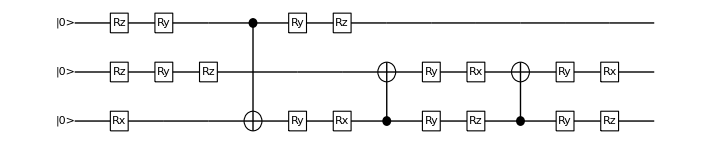

```mathematica
PrintCircuit[gatelist]
```

Note that one gets the same output calling DecIsometry[state] in the considered case.

```mathematica
DecIsometry[state]==StatePreparation[state]
```

True

```mathematica
outstate=CreateOperationFromGateList[gatelist];outstate//MatrixForm
```

(0.0289672-0.0580806 ⅈ
0.0242736+0.407099 ⅈ
0.0125993-0.254175 ⅈ
-0.129065-0.0306737 ⅈ
-0.093767-0.0895678 ⅈ
-0.119618-0.444079 ⅈ
0.635988+0.167483 ⅈ
0.103322+0.2749 ⅈ)

This is equal to the state up to phase

```mathematica
Chop[outstate/outstate[[1,1]]*state[[1,1]]-state]
```

{{0},{0},{0},{0},{0},{0},{0},{0}}

Alternatively, one can decompose a state using uniformly controlled gates by calling the column by column decomposition.  This requires one CNOT gate more in the considered case (but lowers the running time for large states).

```mathematica
gatelist=ColumnByColumnDec[state]
```

{{5,0,3},{5,0,2},{5,0,1},{3,2.16679,3},{2,1.81917,3},{3,2.84907,3},{3,3.04474,2},{2,1.06932,2},{3,3.51884,2},{2,4.19546,1},{3,3.81901,1},{0,1,2},{2,2.89685,2},{1,1.67253,2},{0,2,3},{2,0.507248,3},{1,5.4692,3},{0,1,3},{2,1.30412,3},{1,0.65683,3},{0,2,3},{2,0.213841,3},{1,2.27656,3}}

```mathematica
CNOTCount[gatelist]
```

4

We can also use a special decomposition for sparse states

```mathematica
state=PickRandomSparsePsi[2^7,2^3]
```

SparseArray[…]

```mathematica
Normal[state]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-0.192682-0.0643404 ⅈ},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0.0505958+0.246484 ⅈ},{0},{0},{-0.104806+0.119225 ⅈ},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0.439252-0.194465 ⅈ},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-0.113392-0.244399 ⅈ},{0},{0},{0},{0},{0},{0},{-0.0826466+0.321054 ⅈ},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-0.458137+0.152518 ⅈ},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0.390774+0.266667 ⅈ},{0},{0},{0}}

```mathematica
Length[gatelist=SparseStatePreparation[state]]
```

149

```mathematica
out=Chop[CreateOperationFromGateList[gatelist]];Chop[out*DeleteCases[Flatten[Normal[state]],0][[1]]/DeleteCases[Flatten[Normal[out]],0][[1]]-state]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

Dense state preparation is worse:

```mathematica
Length[StatePreparation[state]]
```

374

### Analytic calculations

We can also do analytic calculations

```mathematica
u={{1,0,0,1},{0,1,1,0},{-1,0,0,1},{0,1,-1,0}}/2^(1/2)
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{-1/(√2),0,0,1/(√2)},{0,1/(√2),-1/(√2),0}}

```mathematica
gatelist=QSD[u]
```

{{3,π/2,2},{2,π/2,2},{3,π/2,2},{3,π/2,1},{2,π/2,1},{0,2,1},{3,π/2,1},{1,π/2,2},{3,(3 π)/2,2},{0,2,1},{2,π,1},{3,(3 π)/2,1}}

```mathematica
outu=CreateOperationFromGateList[gatelist];Simplify[outu/outu[[1,1]]*u[[1,1]]-u]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
gatelist=ColumnByColumnDec[u]
```

{{3,π/2,2},{3,π/2,1},{0,2,1},{3,(3 π)/2,1},{0,2,1},{3,π/2,1},{2,π/2,2},{3,π/2,2},{0,1,2},{3,(3 π)/2,2},{2,(3 π)/2,2},{0,2,1},{2,π/2,1}}

```mathematica
outu=CreateOperationFromGateList[gatelist];Simplify[outu/outu[[1,1]]*u[[1,1]]-u]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Print Circuit can also be used to show the output

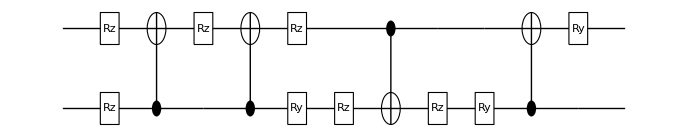

```mathematica
PrintCircuit[gatelist]
```

The option AnglePrecision->1 shows the angles (because they are exact, any precision above 0 can be used)

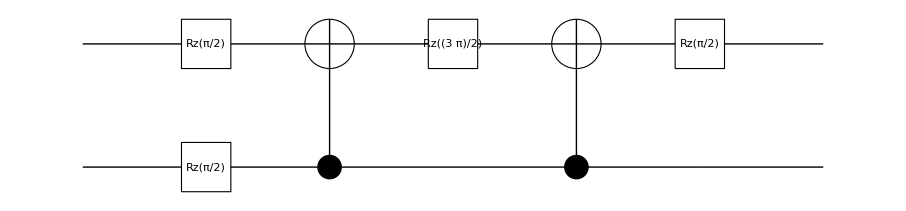

```mathematica
PrintCircuit[Take[gatelist,6],AnglePrecision->1]
```

If non-exact output is desired, can use NGateList

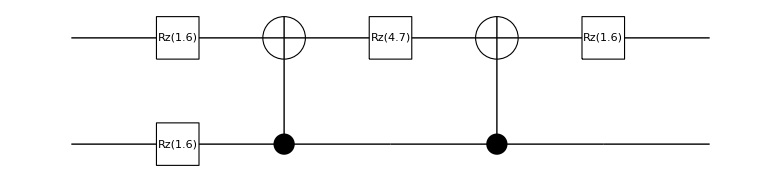

```mathematica
PrintCircuit[Take[NGateList[gatelist],6],AnglePrecision->2]
```

```mathematica
LatexQCircuit[Take[gatelist,6],AnglePrecision->2]
```

{
& \qw  & \gate{R_z(\textnormal{$\frac{\pi }{2}$})} & \targ & \gate{R_z(\textnormal{$\frac{3 \pi }{2}$})} & \targ & \gate{R_z(\textnormal{$\frac{\pi }{2}$})} & \qw  \\
& \qw  & \gate{R_z(\textnormal{$\frac{\pi }{2}$})} & \ctrl{-1} & \qw  & \ctrl{-1} & \qw  & \qw  
}

The exact computations rapidly become time consuming

```mathematica
u={{5/(3 √26),1/(3 √26)},{-1/(√26),5/(√26)},{(5 √(2/13))/3,(√(2/13))/3},{(5 √(2/13))/3,(√(2/13))/3}};
```

```mathematica
CT[u].u
```

{{1,0},{0,1}}

```mathematica
Timing[gatelist=ColumnByColumnDec[u]]
```

{8.87678,{{5,0,1},{3,π,2},{3,(3 π)/4,1},{2,π-2 ArcTan[(1+√2)^2],1},{3,π,1},{0,2,1},{2,2 ArcSec[√(18-12 √2)],1},{2,π-2 ArcTan[1/5 (3+√34)],2},{3,π,2},{0,1,2},{2,π/4,2},{2,π+2 ArcCot[10/(√17)],1},{0,1,2},{2,π-2 ArcCot[1/4 (-1+√17)],2}}}

The output matches the original isometry (up to phase)

```mathematica
Timing[outu=CreateOperationFromGateList[gatelist]]
```

{102.818,{{(5 (-1)^(7/8))/(3 √26),(-1)^(7/8)/(3 √26)},{-(-1)^(7/8)/(√26),(5 (-1)^(7/8))/(√26)},{5/3 (-1)^(7/8) √(2/13),1/3 (-1)^(7/8) √(2/13)},{5/3 (-1)^(7/8) √(2/13),1/3 (-1)^(7/8) √(2/13)}}}

```mathematica
FullSimplify[outu/outu[[1,1]]*u[[1,1]]-u]//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0)

Generating the operator involves attempts to simplify so can be slow.  The option FullSimp->False sometimes yields just as good a result after a final simplification (and can be faster, even including the final simplification):

```mathematica
Timing[outu=FullSimplify[CreateOperationFromGateList[gatelist,FullSimp->False]]]
```

{72.3593,{{(5 (-1)^(7/8))/(3 √26),(-1)^(7/8)/(3 √26)},{-(-1)^(7/8)/(√26),(5 (-1)^(7/8))/(√26)},{5/3 (-1)^(7/8) √(2/13),1/3 (-1)^(7/8) √(2/13)},{5/3 (-1)^(7/8) √(2/13),1/3 (-1)^(7/8) √(2/13)}}}

```mathematica
FullSimplify[outu/outu[[1,1]]*u[[1,1]]-u]//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0)

Using the option Simp->False can be faster (but gives a longer sequence):

```mathematica
Timing[gatelist=ColumnByColumnDec[u,Simp->False]]
```

{3.66537,{{5,0,1},{3,π/2,2},{3,π/4,1},{2,-π/2,1},{3,-ArcTan[2 √2],1},{0,2,1},{3,-π+ArcTan[2 √2],1},{2,-π/2,1},{3,π/2,1},{3,0,2},{2,-π/2,2},{3,-1/2 ArcTan[15/8],2},{0,1,2},{3,-π+1/2 ArcTan[15/8],2},{2,-π/2,2},{3,0,2},{3,0,1},{2,-π+2 ArcCot[10/(√17)],1},{3,0,1},{3,π,2},{2,-π/2,2},{3,-ArcTan[4],2},{0,1,2},{3,-π+ArcCot[4],2},{2,-π/2,2},{3,π/2,2}}}

By comparison, the numerical version is almost instantaneous

```mathematica
Timing[gatelist=ColumnByColumnDec[N[u]]]
```

{0.026088,{{5,0,1},{3,3.14159,2},{3,2.35619,1},{2,0.339837,1},{3,3.14159,1},{0,2,1},{2,0.339837,1},{2,4.17197,2},{0,1,2},{3,3.14159,2},{2,3.92699,2},{2,3.92374,1},{0,1,2},{2,1.32582,2}}}

Again, the output matches:

```mathematica
outu=CreateOperationFromGateList[gatelist];Chop[outu/outu[[1,1]]*u[[1,1]]]//MatrixForm
```

(0.32686 | 0.065372
-0.196116 | 0.980581
0.65372 | 0.130744
0.65372 | 0.130744)

```mathematica
N[u]//MatrixForm
```

(0.32686 | 0.065372
-0.196116 | 0.980581
0.65372 | 0.130744
0.65372 | 0.130744)

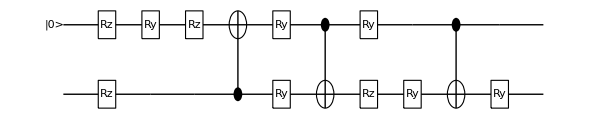

```mathematica
PrintCircuit[gatelist]
```

#### Using the Knill decomposition for analytic calculations

The Knill decomposition is not good at handling analytic calculations at present. However, unitaries of a very simple form can be decomposed within a reasonable time.

```mathematica
u= {{ⅇ^((4 ⅈ π)/5),0,0,0},{0,ⅇ^((2 ⅈ π)/3),0,0},{0,0,ⅇ^((3 ⅈ π)/5),0},{0,0,0,ⅇ^((7 ⅈ π)/15)}};
```

```mathematica
Timing[gatelist=KnillDec[u]]
```

{0.151672,{{3,π,2},{2,π,2},{3,π,1},{2,π,1},{0,1,2},{3,(7 π)/30,2},{0,2,1},{3,(7 π)/30,1},{0,2,1},{3,(7 π)/30,1},{0,1,2},{2,π,2},{3,π,2},{0,1,2},{3,(3 π)/10,2},{0,2,1},{3,(3 π)/10,1},{0,2,1},{3,(3 π)/10,1},{0,1,2},{2,π,2},{3,π,2},{2,π,1},{3,π,1},{0,1,2},{3,π/3,2},{0,2,1},{3,π/3,1},{0,2,1},{3,π/3,1},{0,1,2},{2,π,2},{3,π,2},{0,1,2},{3,(2 π)/5,2},{0,2,1},{3,(2 π)/5,1},{0,2,1},{3,(2 π)/5,1},{0,1,2}}}

#### Sparse states analytically

For sparse states we can generate an exact one using FPickRandomSparsePsi

```mathematica
state=FPickRandomSparsePsi[32,4,3];Normal[state]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{3 √(2/79)},{9/(√158)},{0},{2 √(2/79)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{5/(√158)},{0},{0}}

```mathematica
gatelist=SparseStatePreparation[state]
```

{{5,0,1},{5,0,2},{5,0,3},{5,0,4},{5,0,5},{2,2 π-2 ArcTan[√((79-10 √58)/(79+10 √58))],4},{2,(7 π)/4,2},{3,π,1},{2,π,1},{0,4,5},{2,π-2 ArcCot[1/37 (-9+5 √58)],5},{2,1/2 (π-ArcTan[627/364]),4},{3,π,4},{0,4,2},{2,(7 π)/4,2},{0,5,2},{2,π/4,2},{2,π,5},{0,4,2},{2,π/4,2},{0,2,5},{0,2,4},{0,2,3}}

```mathematica
out=CreateOperationFromGateList[gatelist,FullSimp->False];FullSimplify[out*DeleteCases[Flatten[Normal[state]],0][[1]]/DeleteCases[Flatten[Normal[out]],0][[1]]-state]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

### Performance for different system sizes

Numerically we are able to work with large systems quickly

```mathematica
u=PickRandomUnitary[2^5];
```

```mathematica
Timing[gatelist=DecIsometryGeneric[u]][[1]]
```

3.32098

```mathematica
Length[gatelist]
```

1677

```mathematica
CNOTCount[gatelist]
```

444

Note that DecIsometryGeneric is faster than DecIsometry and with the same CNOT count for our generic unitary

```mathematica
Timing[gatelist=DecIsometry[u]][[1]]
```

139.898

```mathematica
Length[gatelist]
```

1551

```mathematica
CNOTCount[gatelist]
```

444

The run time of DecIsometry can be lowered using the option SpeedUp->True (which may lead to higher gate counts in very rare cases)

```mathematica
Timing[gatelist=DecIsometry[u,SpeedUp->True]][[1]]
```

29.7967

```mathematica
Length[gatelist]
```

1551

```mathematica
CNOTCount[gatelist]
```

444

Increasing the number of qubits...

```mathematica
u=PickRandomUnitary[2^6];
```

```mathematica
Timing[gatelist=DecIsometryGeneric[u]][[1]]
```

13.7097

```mathematica
Length[gatelist]
```

6893

```mathematica
CNOTCount[gatelist]
```

1868

```mathematica
u=PickRandomUnitary[2^7];
```

```mathematica
Timing[gatelist=DecIsometryGeneric[u]][[1]]
```

58.4628

```mathematica
Length[gatelist]
```

27949

```mathematica
CNOTCount[gatelist]
```

7660

### Decomposing channels

We can also decompose channels. Take a channel from 1 qubit to 2 qubits with 10 Kraus operators

```mathematica
chan=RPickRandomChannel[2,4,10];
```

Check that it is a valid channel

```mathematica
Chop[Sum[CT[chan[[i]]].chan[[i]],{i,1,10}]]
```

{{1.,0},{0,1.}}

Its action on a density operator rho is

```mathematica
rho=RPickRandomRho[2];
```

```mathematica
rhoout=Chop[Sum[chan[[i]].rho.CT[chan[[i]]],{i,1,10}]]
```

{{0.156612,-0.0322629,-0.0730327,-0.0939991},{-0.0322629,0.193459,0.0569057,-0.068146},{-0.0730327,0.0569057,0.358533,-0.105076},{-0.0939991,-0.068146,-0.105076,0.291396}}

This channel has more than the maximum number of Kraus operators, so we can compress it to a smaller representation of the same channel

```mathematica
chan2=MinimizeKrausRank[chan];Length[chan2]
```

8

The action on rho is the same:

```mathematica
Chop[rhoout-Sum[chan2[[i]].rho.CT[chan2[[i]]],{i,1,Length[chan2]}]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
gatelist=DecChannelInQCM[chan2];
```

```mathematica
Length[gatelist]
```

165

The output is quite long, but the first and last 20 gates are displayed below. Note the trace out circuit elements, and the indication of ancilla.

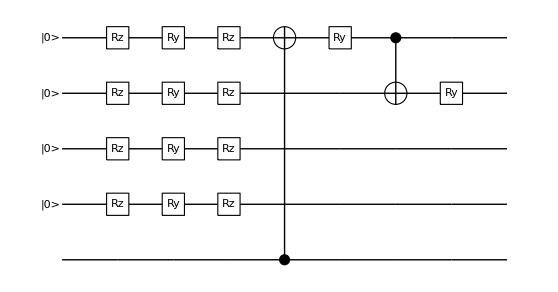

```mathematica
PrintCircuit[Take[gatelist,20]]
```

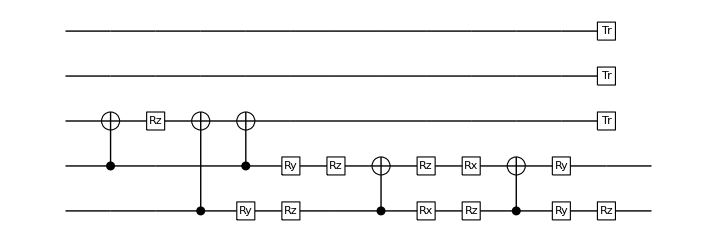

```mathematica
PrintCircuit[Take[gatelist,-20]]
```

We can reconstruct the channel as follows.

First remove the traces from the gatelist

```mathematica
gatelist2=DeleteCases[gatelist,{TrOut[1][[1]],_,_}];
```

```mathematica
Length[gatelist2]
```

162

We have a channel from 1 to 2 qubits, so the first 4 qubits of the input start in state 0. The partial traces can be used to generate Kraus operators by taking the projectors onto the computational basis:

```mathematica
chanout={};For[i=0,i≤7,i++,chanout=Insert[chanout,(BraV[i,2^3]⊗IdentityMatrix[4]).CreateOperationFromGateList[gatelist2],-1]]
```

Check that it has the same action

```mathematica
Chop[rhoout-Sum[chanout[[i]].rho.CT[chanout[[i]]],{i,1,Length[chanout]}]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

We can also use CreateOperationFromGateList

```mathematica
chanout2=CreateOperationFromGateList[gatelist];
```

```mathematica
Chop[chanout2-chanout]
```

{{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}}}

### Decomposing POVMs

Similarly we can implement a POVM. Choose a random POVM on 1 qubit with 3 elements

```mathematica
POVM=RPickRandomPOVM[2,3]
```

{{{0.340541,-0.0506885},{-0.0506885,0.331296}},{{0.00186299,0.0137921},{0.0137921,0.119649}},{{0.657596,0.0368964},{0.0368964,0.549055}}}

Check that it is a valid POVM: its elements should sum to identity and all operators should be positive

```mathematica
Chop[Sum[POVM[[i]],{i,1,3}]]
```

{{1.,0},{0,1.}}

```mathematica
For[i=1,i≤3,i++,Print[Min[Eigenvalues[POVM[[i]]]]]]
```

0.28502

0.000269566

0.5377

We now decompose it into a list of gates

```mathematica
gatelist=DecPOVMInQCM[POVM];
```

```mathematica
Length[gatelist]
```

43

Printing the last  part of the circuit shows the measured qubits

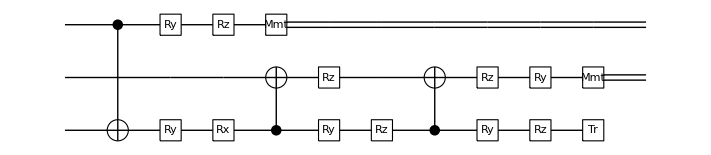

```mathematica
PrintCircuit[Take[gatelist,-17]]
```

To get back the POVM from the gatelist:

```mathematica
pt1=(BraV[0,2]⊗BraV[0,2]⊗IdentityMatrix[2]).CreateOperationFromGateList[DeleteCases[gatelist,{TrOut[1][[1]],_,_}]];pt2=(BraV[0,2]⊗BraV[1,2]⊗IdentityMatrix[2]).CreateOperationFromGateList[DeleteCases[gatelist,{TrOut[1][[1]],_,_}]];pt3=(BraV[1,2]⊗BraV[0,2]⊗IdentityMatrix[2]).CreateOperationFromGateList[DeleteCases[gatelist,{TrOut[1][[1]],_,_}]];pt4=(BraV[1,2]⊗BraV[1,2]⊗IdentityMatrix[2]).CreateOperationFromGateList[DeleteCases[gatelist,{TrOut[1][[1]],_,_}]];
```

```mathematica
POVMout=Chop[{pt1.CT[pt1],CT[pt2].pt2,CT[pt3].pt3,CT[pt4].pt4}]
```

{{{0.340541,-0.0506885},{-0.0506885,0.331296}},{{0.00186299,0.0137921},{0.0137921,0.119649}},{{0.657596,0.0368964},{0.0368964,0.549055}},{{0,0},{0,0}}}

The zero POVM element can be dropped. We then get the same POVM as we started with

```mathematica
Chop[Drop[POVMout,-1]-POVM]
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}

We could also use CreatePOVMFromGateList

```mathematica
Chop[CreatePOVMFromGateList[gatelist]-POVM]
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}

CreatePOVMFromGateList automatically removes zero POVM elements if they occur at the end of the list of POVM elements. To avoid this, use the option DropZero->”None”.

```mathematica
Chop[CreatePOVMFromGateList[gatelist,DropZero->"None"]]
```

{{{0.340541,-0.0506885},{-0.0506885,0.331296}},{{0.00186299,0.0137921},{0.0137921,0.119649}},{{0.657596,0.0368964},{0.0368964,0.549055}},{{0,0},{0,0}}}

The option DropZero->”All” removes all POVM elements.  Note that this can make it difficult to identify POVM elements with outcomes (in the case where zero elements are in the middle of the list of POVM elements).

```mathematica
POVM2=Insert[POVM,{{0,0},{0,0}},2]
```

{{{0.340541,-0.0506885},{-0.0506885,0.331296}},{{0,0},{0,0}},{{0.00186299,0.0137921},{0.0137921,0.119649}},{{0.657596,0.0368964},{0.0368964,0.549055}}}

```mathematica
gatelist2=DecPOVMInQCM[POVM2];
```

```mathematica
Chop[CreatePOVMFromGateList[gatelist2,DropZero->"All"]]
```

{{{0.340541,-0.0506885},{-0.0506885,0.331296}},{{0.00186299,0.0137921},{0.0137921,0.119649}},{{0.657596,0.0368964},{0.0368964,0.549055}}}

```mathematica
Chop[CreatePOVMFromGateList[gatelist2]]
```

{{{0.340541,-0.0506885},{-0.0506885,0.331296}},{{0,0},{0,0}},{{0.00186299,0.0137921},{0.0137921,0.119649}},{{0.657596,0.0368964},{0.0368964,0.549055}}}

### Constructing circuits

We can also build our own circuits and use the code to simplify them

```mathematica
gatelist={CNOT[1,2],CNOT[2,1],Rz[π/2,3],Rz[π/2,1],Rx[π/4,2],CNOT[1,2],Rz[π/4,1],CNOT[3,2],Rx[π/8,2],Ry[π/3,3],Rx[π/4,3],Rz[π/6,3],CNOT[1,2]}
```

{{0,1,2},{0,2,1},{3,π/2,3},{3,π/2,1},{1,π/4,2},{0,1,2},{3,π/4,1},{0,3,2},{1,π/8,2},{2,π/3,3},{1,π/4,3},{3,π/6,3},{0,1,2}}

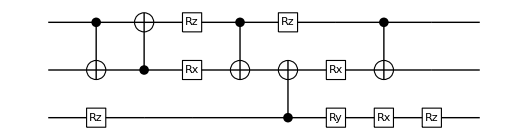

```mathematica
PrintCircuit[gatelist]
```

```mathematica
Timing[gatelist2=NSimplifyGateList[gatelist]]
```

{0.004316,{{3,0.713724,3},{0,1,2},{0,2,1},{3,2.35619,1},{1,1.1781,2},{0,3,2},{2,1.20943,3},{3,0.911195,3}}}

We could also simplify the gate sequence analytically, by calling SimplifyGateList[gatelist]]. But this takes much longer:

```mathematica
Timing[gatelist2=SimplifyGateList[gatelist]]
```

{3.44002,{{3,1/2 ArcTan[4 √3],3},{0,1,2},{0,2,1},{3,(3 π)/4,1},{1,(3 π)/8,2},{0,3,2},{2,π-2 ArcTan[√(1/7 (9+4 √2))],3},{3,ArcCot[17/(√(243+168 √2))],3}}}

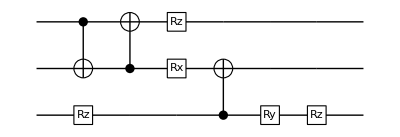

```mathematica
PrintCircuit[gatelist2]
```

```mathematica
out=N[CreateOperationFromGateList[gatelist,FullSimp->False]];out2=N[CreateOperationFromGateList[gatelist2,FullSimp->False]];
```

```mathematica
Chop[out2/out2[[1,1]]*out[[1,1]]-out]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

For simple constructions, ColumnByColumnDec is often best

```mathematica
u=NCreateOperationFromGateList[{CNOT[1,2],Ry[π/4,3],Rx[π/8,3],CNOT[2,3],Ry[π/4,2],CNOT[1,2]}]
```

{{0.837153-0.0689748 ⅈ,0.34676+0.16652 ⅈ,-0.143633+0.0689748 ⅈ,0.34676+0.0285703 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.34676+0.16652 ⅈ,0.837153+0.0689748 ⅈ,0.34676-0.0285703 ⅈ,0.143633+0.0689748 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.34676+0.0285703 ⅈ,-0.143633-0.0689748 ⅈ,-0.34676+0.16652 ⅈ,0.837153+0.0689748 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.143633-0.0689748 ⅈ,-0.34676-0.0285703 ⅈ,0.837153-0.0689748 ⅈ,0.34676+0.16652 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.34676+0.16652 ⅈ,0.837153+0.0689748 ⅈ,-0.34676+0.0285703 ⅈ,-0.143633-0.0689748 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.837153-0.0689748 ⅈ,0.34676+0.16652 ⅈ,0.143633-0.0689748 ⅈ,-0.34676-0.0285703 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.143633+0.0689748 ⅈ,0.34676+0.0285703 ⅈ,0.837153-0.0689748 ⅈ,0.34676+0.16652 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.34676-0.0285703 ⅈ,0.143633+0.0689748 ⅈ,-0.34676+0.16652 ⅈ,0.837153+0.0689748 ⅈ}}

```mathematica
CNOTCount[ColumnByColumnDec[u]]
```

14

```mathematica
CNOTCount[QSD[u]]
```

18

```mathematica
CNOTCount[KnillDec[u]]
```

91

### We can also generate quantum instruments

If we both trace out and measure, we get a quantum instrument

```mathematica
gatelist={CNOT[1,2],CNOT[2,1],Rz[π/2,3],Rz[π/2,1],Rx[π/4,2],CNOT[1,2],Rz[π/4,1],CNOT[3,2],Rx[π/8,2],Ry[π/3,3],Rx[π/4,3],Rz[π/6,3],CNOT[1,2],TrOut[1],Mmt[2]};gatelist=NGateList[gatelist]
```

{{0,1,2},{0,2,1},{3,1.5708,3},{3,1.5708,1},{1,0.785398,2},{0,1,2},{3,0.785398,1},{0,3,2},{1,0.392699,2},{2,1.0472,3},{1,0.785398,3},{3,0.523599,3},{0,1,2},{4,0,1},{4,1,2}}

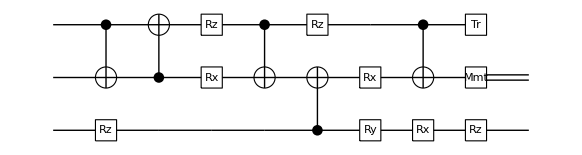

```mathematica
PrintCircuit[gatelist]
```

```mathematica
inst=Chop[CreateOperationFromGateList[gatelist]]
```

{{{{-0.278767+0.624638 ⅈ,-0.302308+0.0915189 ⅈ,0,0,-0.41737-0.186266 ⅈ,0.136968+0.452435 ⅈ,0,0},{-0.223069-0.416771 ⅈ,-0.163415+0.426835 ⅈ,0,0,0.278477-0.14905 ⅈ,0.638804+0.244568 ⅈ,0,0}},{{0,0,0.163415+0.426835 ⅈ,0.223069-0.416771 ⅈ,0,0,0.638804-0.244568 ⅈ,0.278477+0.14905 ⅈ},{0,0,-0.302308-0.0915189 ⅈ,-0.278767-0.624638 ⅈ,0,0,-0.136968+0.452435 ⅈ,0.41737-0.186266 ⅈ}}},{{{-0.41737-0.186266 ⅈ,0.136968+0.452435 ⅈ,0,0,-0.278767+0.624638 ⅈ,-0.302308+0.0915189 ⅈ,0,0},{0.278477-0.14905 ⅈ,0.638804+0.244568 ⅈ,0,0,-0.223069-0.416771 ⅈ,-0.163415+0.426835 ⅈ,0,0}},{{0,0,0.638804-0.244568 ⅈ,0.278477+0.14905 ⅈ,0,0,0.163415+0.426835 ⅈ,0.223069-0.416771 ⅈ},{0,0,-0.136968+0.452435 ⅈ,0.41737-0.186266 ⅈ,0,0,-0.302308-0.0915189 ⅈ,-0.278767-0.624638 ⅈ}}}}

Each part of this should be a trace decreasing completely positive map such that the combined channel is trace preserving:

```mathematica
{chan1,chan2}=inst;
```

```mathematica
Chop[Sum[CT[chan1[[i]]].chan1[[i]],{i,1,Length[chan1]}]+Sum[CT[chan2[[i]]].chan2[[i]],{i,1,Length[chan1]}]]
```

{{1.,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0},{0,0,0,1.,0,0,0,0},{0,0,0,0,1.,0,0,0},{0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,1.}}

If we care about the measurement, we can instead construct the POVM

```mathematica
POVM=Chop[CreatePOVMFromGateList[gatelist]]
```

{{{0.691342,0,0,0,0.+0.46194 ⅈ,0,0,0},{0,0.308658,0,0,0,0.-0.46194 ⅈ,0,0},{0,0,0.308658,0,0,0,0.-0.46194 ⅈ,0},{0,0,0,0.691342,0,0,0,0.+0.46194 ⅈ},{0.-0.46194 ⅈ,0,0,0,0.308658,0,0,0},{0,0.+0.46194 ⅈ,0,0,0,0.691342,0,0},{0,0,0.+0.46194 ⅈ,0,0,0,0.691342,0},{0,0,0,0.-0.46194 ⅈ,0,0,0,0.308658}},{{0.308658,0,0,0,0.-0.46194 ⅈ,0,0,0},{0,0.691342,0,0,0,0.+0.46194 ⅈ,0,0},{0,0,0.691342,0,0,0,0.+0.46194 ⅈ,0},{0,0,0,0.308658,0,0,0,0.-0.46194 ⅈ},{0.+0.46194 ⅈ,0,0,0,0.691342,0,0,0},{0,0.-0.46194 ⅈ,0,0,0,0.308658,0,0},{0,0,0.-0.46194 ⅈ,0,0,0,0.308658,0},{0,0,0,0.+0.46194 ⅈ,0,0,0,0.691342}}}

These agree with the channels

```mathematica
Chop[POVM[[1]]-Sum[CT[chan1[[i]]].chan1[[i]],{i,1,Length[chan1]}]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Chop[POVM[[2]]-Sum[CT[chan2[[i]]].chan2[[i]],{i,1,Length[chan2]}]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

The following command provides a convenient way to see the action of an instrument:

```mathematica
InstrumentActionOnRho[instr_, rho_] := Module[{i, j, proba, out, listProba = {}, listOut = {}, chan},
  For[i=1, i<=Length[instr], i++,
    chan = instr[[i]];
    out = Chop[Sum[chan[[j]].rho.CT[chan[[j]]], {j, 1, Length[chan]}]];
    proba = Tr[out];
    If[!(proba == 0), Print["Output state: ", (out/proba)//MatrixForm, " with probability: ", proba]]
  ]
]
```

```mathematica
rho=PickRandomRho[2^3];
```

```mathematica
InstrumentActionOnRho[inst,rho]
```

Output state: (0.437384 | 0.0706402+0.130191 ⅈ
0.0706402-0.130191 ⅈ | 0.562616) with probability: 0.362323

Output state: (0.531326 | -0.041039+0.00257617 ⅈ
-0.041039-0.00257617 ⅈ | 0.468674) with probability: 0.637677

We can also generate random instruments. The following gives an instrument from 1 qubit to 2 qubits comprising two channels each with 4 Kraus operators

```mathematica
inst=PickRandomInstrument[2^1,2^2,2,4];
```

```mathematica
Dimensions[inst]
```

{2,4,4,2}

```mathematica
gatelist= DecInstrumentInQCM[inst]
```

{{5,0,4},{5,0,3},{5,0,2},{5,0,1},{3,4.34337,5},{3,2.42515,4},{2,1.19451,4},{3,3.44573,4},{3,4.27875,3},{2,1.48461,3},{3,3.20053,3},{3,0.797739,2},{2,1.68857,2},{3,3.13921,2},{3,5.16286,1},{2,1.27898,1},{3,2.56862,1},{0,5,1},{2,1.22747,1},{1,5.73725,1},{0,1,2},{2,0.847438,2},{1,3.24063,2},{0,5,2},{2,2.29785,2},{1,0.0683241,2},{0,2,3},{2,0.221308,3},{1,0.13993,3},{0,1,3},{2,0.304034,3},{1,1.69867,3},{0,2,3},{2,0.877521,3},{1,4.28677,3},{0,5,3},{2,1.11065,3},{1,0.887282,3},{0,3,4},{2,0.343161,4},{1,6.21846,4},{0,2,4},{2,0.0597111,4},{1,6.19924,4},{0,3,4},{2,0.409615,4},{1,5.46313,4},{0,1,4},{2,0.608413,4},{1,5.29906,4},{0,3,4},{2,0.449197,4},{1,3.64129,4},{0,2,4},{2,0.703449,4},{1,1.33571,4},{0,3,4},{2,2.23958,4},{1,1.09957,4},{0,5,4},{2,1.49483,4},{1,5.24958,4},{2,1.48292,5},{3,3.56777,5},{0,4,5},{2,0.170439,5},{1,4.86572,5},{0,3,5},{2,0.173606,5},{1,6.18889,5},{0,4,5},{2,0.332411,5},{1,0.440267,5},{0,2,5},{2,0.361291,5},{1,3.2298,5},{0,4,5},{2,0.238022,5},{1,5.53758,5},{0,3,5},{2,0.230073,5},{1,4.91284,5},{0,4,5},{2,0.0807644,5},{1,5.23973,5},{0,1,5},{2,0.291542,5},{1,0.347737,5},{2,5.53922,1},{0,4,5},{2,0.0163538,5},{1,3.22436,5},{0,3,5},{2,0.42777,5},{1,5.0807,5},{0,4,5},{2,0.569033,5},{1,1.756,5},{0,2,5},{2,0.454143,5},{1,1.25346,5},{1,5.95247,2},{0,4,5},{2,0.852353,5},{1,0.619962,5},{0,3,5},{2,1.05064,5},{1,4.30126,5},{2,4.97707,3},{0,4,5},{2,1.69959,5},{1,3.51095,5},{1,3.92978,4},{0,1,2},{2,2.03826,2},{1,2.99512,2},{2,0.581167,1},{3,0.157546,1},{0,1,4},{2,0.396371,4},{1,4.18224,4},{2,2.86697,1},{3,6.27326,1},{0,2,5},{2,0.764296,5},{1,5.55293,5},{2,1.59074,2},{3,6.1552,2},{0,2,1},{2,1.07373,1},{1,3.08956,1},{2,1.39496,2},{3,3.279,2},{0,2,1},{2,2.12413,1},{1,0.130949,1},{2,1.55874,2},{3,4.03009,2},{0,5,4},{3,5.28754,4},{1,2.67677,4},{1,1.49124,5},{3,5.33614,5},{0,5,4},{2,2.19295,4},{1,5.1028,4},{2,2.09593,5},{3,3.81893,5},{0,4,3},{2,6.08969,3},{0,5,3},{2,0.893361,3},{2,1.77618,5},{3,5.97223,5},{0,4,3},{2,0.415431,3},{2,0.968663,4},{3,0.13665,4},{0,5,4},{3,5.59622,4},{1,3.31184,4},{1,5.03923,5},{3,4.16589,5},{0,5,4},{2,1.40879,4},{1,5.6642,4},{2,1.27699,5},{3,4.1151,5},{0,5,3},{3,0.822257,3},{0,4,3},{3,1.69092,3},{0,5,3},{3,0.3341,3},{2,1.44636,5},{3,4.29299,5},{0,4,3},{3,0.208031,3},{2,1.39166,4},{3,0.141853,4},{0,5,4},{3,5.46346,4},{1,0.277055,4},{1,4.87381,5},{3,1.22032,5},{0,5,4},{2,2.21245,4},{1,3.92642,4},{2,1.04874,5},{3,1.27476,5},{0,4,5},{3,0.0283893,5},{4,1,1},{4,0,2},{4,0,3}}

The start of the circuit is shown below

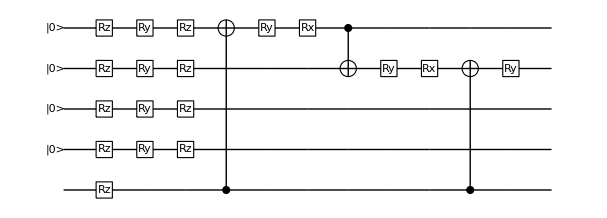

```mathematica
PrintCircuit[Take[gatelist,25]]
```

And here is the end of the circuit

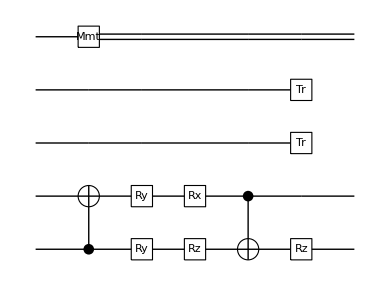

```mathematica
PrintCircuit[Take[gatelist,-10]]
```

To get back the instrument

```mathematica
instout=CreateOperationFromGateList[gatelist];
```

```mathematica
Dimensions[instout]
```

{2,4,4,2}

To check these are the same instrument we can extract the individual channels and confirm that they have the same Choi states:

```mathematica
{chan1,chan2}=inst;{chanout1,chanout2}=instout;
```

```mathematica
Chop[KrausToChoi[chan1]-KrausToChoi[chanout1]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Chop[KrausToChoi[chan2]-KrausToChoi[chanout2]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

We can also observe the same action on a randomly chosen input

```mathematica
rho=PickRandomRho[2];
```

```mathematica
InstrumentActionOnRho[inst,rho]
```

Output state: (0.109075 | 0.0605816-0.0314489 ⅈ | -0.0549166+0.0539702 ⅈ | 0.0165014+0.0626666 ⅈ
0.0605816+0.0314489 ⅈ | 0.217269 | -0.12019-0.0873199 ⅈ | -0.0707872+0.0636828 ⅈ
-0.0549166-0.0539702 ⅈ | -0.12019+0.0873199 ⅈ | 0.337591 | 0.126336-0.200746 ⅈ
0.0165014-0.0626666 ⅈ | -0.0707872-0.0636828 ⅈ | 0.126336+0.200746 ⅈ | 0.336065) with probability: 0.375431

Output state: (0.190085 | -0.0767031+0.111526 ⅈ | 0.0572249+0.0509582 ⅈ | 0.00601064-0.168052 ⅈ
-0.0767031-0.111526 ⅈ | 0.244049 | 0.0044573-0.0608909 ⅈ | -0.10898+0.0634701 ⅈ
0.0572249-0.0509582 ⅈ | 0.0044573+0.0608909 ⅈ | 0.0874478 | -0.0271749+0.0303012 ⅈ
0.00601064+0.168052 ⅈ | -0.10898-0.0634701 ⅈ | -0.0271749-0.0303012 ⅈ | 0.478418) with probability: 0.624569

```mathematica
InstrumentActionOnRho[instout,rho]
```

Output state: (0.109075 | 0.0605816-0.0314489 ⅈ | -0.0549166+0.0539702 ⅈ | 0.0165014+0.0626666 ⅈ
0.0605816+0.0314489 ⅈ | 0.217269 | -0.12019-0.0873199 ⅈ | -0.0707872+0.0636828 ⅈ
-0.0549166-0.0539702 ⅈ | -0.12019+0.0873199 ⅈ | 0.337591 | 0.126336-0.200746 ⅈ
0.0165014-0.0626666 ⅈ | -0.0707872-0.0636828 ⅈ | 0.126336+0.200746 ⅈ | 0.336065) with probability: 0.375431

Output state: (0.190085 | -0.0767031+0.111526 ⅈ | 0.0572249+0.0509582 ⅈ | 0.00601064-0.168052 ⅈ
-0.0767031-0.111526 ⅈ | 0.244049 | 0.0044573-0.0608909 ⅈ | -0.10898+0.0634701 ⅈ
0.0572249-0.0509582 ⅈ | 0.0044573+0.0608909 ⅈ | 0.0874478 | -0.0271749+0.0303012 ⅈ
0.00601064+0.168052 ⅈ | -0.10898-0.0634701 ⅈ | -0.0271749-0.0303012 ⅈ | 0.478418) with probability: 0.624569

To generate an instrument from 1 qubit to 2 comprising three channels with 1, 2 and 3 Kraus operators, use

```mathematica
inst=PickRandomInstrument[2^1,2^2,3,{1,2,3}]
```

{{{{0.140454+0.0441182 ⅈ,0.0655939-0.0817906 ⅈ},{0.217583+0.00854101 ⅈ,-0.408258+0.0592922 ⅈ},{-0.217378+0.0336061 ⅈ,0.0144306+0.148996 ⅈ},{-0.00536285-0.00781289 ⅈ,-0.214174+0.236668 ⅈ}}},{{{0.0347253-0.0200255 ⅈ,-0.0153672-0.0299715 ⅈ},{-0.0345839-0.0714903 ⅈ,-0.198686-0.158965 ⅈ},{-0.0485493+0.136042 ⅈ,0.134924-0.108729 ⅈ},{0.019318-0.081677 ⅈ,0.123394+0.0934528 ⅈ}},{{0.0143343+0.0315964 ⅈ,0.0938482-0.0973706 ⅈ},{0.137173+0.20438 ⅈ,0.141529-0.160104 ⅈ},{-0.0996038-0.0433246 ⅈ,-0.0510681+0.0726152 ⅈ},{-0.150142-0.121066 ⅈ,-0.179011+0.0500737 ⅈ}}},{{{0.233174+0.0773065 ⅈ,-0.175473-0.0596684 ⅈ},{0.244221-0.294831 ⅈ,0.130695+0.0727678 ⅈ},{0.211222-0.103188 ⅈ,0.00614575+0.221308 ⅈ},{-0.240809-0.120098 ⅈ,0.0127687+0.0608324 ⅈ}},{{-0.396924-0.242235 ⅈ,-0.0246251-0.0487635 ⅈ},{0.0273011-0.0514558 ⅈ,0.120804+0.146191 ⅈ},{0.00337462+0.0475122 ⅈ,0.154601-0.101195 ⅈ},{-0.0895567+0.264704 ⅈ,-0.254223+0.0403384 ⅈ}},{{0.0259103-0.0347015 ⅈ,-0.0425445+0.0155988 ⅈ},{0.0973726-0.162556 ⅈ,0.0102396-0.143194 ⅈ},{-0.045422-0.196912 ⅈ,0.0429353-0.328388 ⅈ},{0.0777363-0.128832 ⅈ,-0.173481-0.238499 ⅈ}}}}

### Conversion to another gate library

We can convert to another universal gate library comprising the Molmer-Sorensen gate (XX) and a two-parameter single qubit gate (RGate):

```mathematica
gatelist=DecPOVMInQCM[POVM];
```

```mathematica
XXM[t]//MatrixForm
```

(Cos[t] | 0 | 0 | -ⅈ Sin[t]
0 | Cos[t] | -ⅈ Sin[t] | 0
0 | -ⅈ Sin[t] | Cos[t] | 0
-ⅈ Sin[t] | 0 | 0 | Cos[t])

```mathematica
RGateM[t,p]//MatrixForm
```

(Cos[t/2] | -ⅈ ⅇ^(-ⅈ p) Sin[t/2]
-ⅈ ⅇ^(ⅈ p) Sin[t/2] | Cos[t/2])

To convert an existing gatelist to the new gates, use:

```mathematica
gatelistXX=CNOTRotationsToXXRGates[gatelist]
```

{{5,0,1},{-11,{-1.5708,0},1},{-11,{4.78037,-1.5708},1},{-11,{2.79421,0},2},{-11,{2.66673,-2.30283},2},{-11,{6.10191,0},3},{-11,{4.67988,-1.74917},3},{-11,{π,0},4},{-11,{π/2,-π/2},4},{-10,π/4,{3,2}},{-11,{3.14159,-1.5708},2},{-11,{2 π,-π/2},3},{-10,π/4,{3,2}},{-11,{1.68695,-1.24267},2},{-11,{π,0},3},{-10,π/4,{2,1}},{-11,{4.71239,-1.5708},1},{-11,{3.68962,-2.31665},2},{-10,π/4,{1,2}},{-11,{2.54482,-2.40766},2},{-11,{3.14159,-0.19635},1},{-10,π/4,{3,1}},{-11,{π,-π},1},{-11,{2 π,-π/2},3},{-10,π/4,{3,2}},{-11,{0.804987,-2.90841},2},{-11,{π/2,-π/2},3},{-10,π/4,{4,1}},{-11,{π,-π/4},1},{-11,{2 π,-π/2},4},{-10,π/4,{4,2}},{-11,{5.49779,-3.14159},2},{-11,{π/2,-π/2},4},{-10,π/4,{1,2}},{-11,{1.71777,-1.93629},2},{-11,{π/2,-π/2},1},{4,1,1},{4,0,2},{4,0,3},{4,0,4}}

Check that this is the same POVM:

```mathematica
POVM2=Chop[CreatePOVMFromGateList[gatelistXX]]
```

{{{0.691342,0,0,0,0.+0.46194 ⅈ,0,0,0},{0,0.308658,0,0,0,0.-0.46194 ⅈ,0,0},{0,0,0.308658,0,0,0,0.-0.46194 ⅈ,0},{0,0,0,0.691342,0,0,0,0.+0.46194 ⅈ},{0.-0.46194 ⅈ,0,0,0,0.308658,0,0,0},{0,0.+0.46194 ⅈ,0,0,0,0.691342,0,0},{0,0,0.+0.46194 ⅈ,0,0,0,0.691342,0},{0,0,0,0.-0.46194 ⅈ,0,0,0,0.308658}},{{0.308658,0,0,0,0.-0.46194 ⅈ,0,0,0},{0,0.691342,0,0,0,0.+0.46194 ⅈ,0,0},{0,0,0.691342,0,0,0,0.+0.46194 ⅈ,0},{0,0,0,0.308658,0,0,0,0.-0.46194 ⅈ},{0.+0.46194 ⅈ,0,0,0,0.691342,0,0,0},{0,0.-0.46194 ⅈ,0,0,0,0.308658,0,0},{0,0,0.-0.46194 ⅈ,0,0,0,0.308658,0},{0,0,0,0.+0.46194 ⅈ,0,0,0,0.691342}}}

```mathematica
Chop[POVM2-POVM]
```

{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}

We can also convert back

```mathematica
gatelistback=XXRGatesToCNOTRotations[gatelistXX]
```

{{5,0,1},{2,π,4},{2,π,3},{3,3.32287,3},{3,6.23787,2},{2,1.91818,2},{3,4.71239,2},{3,0.0679794,1},{2,1.5708,1},{3,4.71239,1},{0,3,2},{2,π,2},{1,5.93581,2},{0,3,2},{2,1.52548,2},{1,4.71239,2},{0,2,1},{2,1.5708,1},{1,1.5708,1},{2,1.5708,2},{3,1.5708,2},{0,1,2},{2,1.38952,2},{1,3.14159,2},{2,1.5708,1},{3,5.89049,1},{0,3,1},{0,3,2},{2,0.181278,2},{1,3.14159,2},{2,π,3},{0,4,1},{2,π,1},{1,π/2,1},{0,4,2},{2,π,4},{0,1,2},{2,1.5708,2},{1,0.392699,2},{2,π,1},{4,1,1},{4,0,2},{4,0,3},{4,0,4}}

```mathematica
Chop[CreatePOVMFromGateList[gatelistback]-POVM]
```

{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}

Note that this conversion changes the actual list in general, although the operation remains the same:

```mathematica
Length[gatelistback]
```

44

```mathematica
Length[gatelist]
```

28

### Ordering issues

#### Controlled gates

One has to be careful about gate ordering for controlled gates

Let’s create a gate with qubits 1 and 2 as two controls and qubit 3 as target.

```mathematica
UCG=FullSimplify[CreateUCG[ucgates={RxM[π/2,1],RzM[π/4,1],RyM[π/4,1],IdentityMatrix[2]},{1,2},3,3]];UCG//MatrixForm
```

(1/(√2) | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-1)^(1/8) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(-1)^(7/8) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[π/8] | Sin[π/8] | 0 | 0
0 | 0 | 0 | 0 | -Sin[π/8] | Cos[π/8] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[UCG.CT[UCG]]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

If the first qubits start in state |1> ⊗ |0>, the final qubit is acted on by RyM[π/4,1]:

```mathematica
psi3={{a},{b}};
```

```mathematica
out=UCG.(KetV[1,2]⊗KetV[0,2]⊗psi3);out//MatrixForm
```

(0
0
0
0
a Cos[π/8]+b Sin[π/8]
b Cos[π/8]-a Sin[π/8]
0
0)

The state of the final qubit is

```mathematica
(BraV[1,2]⊗BraV[0,2]⊗IdentityMatrix[2]).out//MatrixForm
```

(a Cos[π/8]+b Sin[π/8]
b Cos[π/8]-a Sin[π/8])

This is the same as

```mathematica
FullSimplify[RyM[π/4,1].psi3]//MatrixForm
```

(a Cos[π/8]+b Sin[π/8]
b Cos[π/8]-a Sin[π/8])

If we instead apply the same gate with controls {2,1} (in effect relabelling the controls)

```mathematica
UCG2=FullSimplify[CreateUCG[{RxM[π/2,1],RzM[π/4,1],RyM[π/4,1],IdentityMatrix[2]},{2,1},3,3]];UCG2//MatrixForm
```

(1/(√2) | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/(√2) | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Cos[π/8] | Sin[π/8] | 0 | 0 | 0 | 0
0 | 0 | -Sin[π/8] | Cos[π/8] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1)^(1/8) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(-1)^(7/8) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

This relabelling is the same as exchanging the first two systems

```mathematica
ExchangeSystems[UCG2,{2,1,3},{2,2,2}]-UCG
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Now if the inputs are |1> ⊗ |0> the action is that of RzM[π/4,1]

```mathematica
out2=UCG2.(KetV[1,2]⊗KetV[0,2]⊗psi3);Simplify[(BraV[1,2]⊗BraV[0,2]⊗IdentityMatrix[2]).out2-RzM[π/4,1].psi3]
```

{{0},{0}}

We can also get back a gate list

```mathematica
gatelist=DecIsometry[N[UCG2]]
```

{{3,4.90874,3},{3,1.5708,2},{3,4.71239,1},{0,2,1},{3,4.71239,1},{0,3,1},{3,1.37445,1},{0,2,1},{3,1.37445,1},{0,3,1},{0,3,2},{3,4.90874,2},{0,3,2},{2,1.76715,3},{3,3.14159,3},{0,2,3},{2,0.19635,3},{0,1,3},{2,0.19635,3},{1,2.01097,3},{0,2,3},{2,0.436759,3},{1,5.80384,3},{0,2,3},{2,0.392699,3},{0,1,3},{2,0.392699,3},{1,4.71239,3},{0,2,3},{3,3.53429,3},{2,4.71239,3}}

This gives the same as making the gate list for UCG and then swapping

```mathematica
gatelist2=RelabelQubits[DecIsometry[N[UCG]],{1,2},{2,1}]
```

{{3,3.33794,3},{3,6.28319,1},{3,6.28319,2},{0,1,2},{0,3,2},{3,6.08684,2},{0,1,2},{3,0.19635,2},{0,3,2},{0,3,1},{3,6.08684,1},{0,3,1},{2,1.37445,3},{3,3.14159,3},{0,1,3},{2,0.19635,3},{1,3.14159,3},{0,2,3},{2,0.19635,3},{1,1.13063,3},{0,1,3},{2,0.436759,3},{1,0.479349,3},{0,1,3},{2,0.392699,3},{0,2,3},{2,0.392699,3},{1,4.71239,3},{0,1,3},{3,3.53429,3},{2,4.71239,3}}

```mathematica
isom=CreateOperationFromGateList[gatelist];isom2=CreateOperationFromGateList[gatelist2];Chop[isom-isom2/isom2[[1,1]]*isom[[1,1]]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Note that in the special case of a uniformly controlled gate, we also provide an adapted method achieving a slighlty lower CNOT counts than DecIsometry.

```mathematica
CNOTCount[gatelist2]
```

12

```mathematica
gateListWithToDiagonal=DecUCGUpToDiagonal[N[ucgates],{2,1},3,3,ReturnDiagonal->True]
```

{{3,0.271058,3},{2,1.76333,3},{3,-2.65158,3},{0,1,3},{3,-1.09003,3},{2,1.52341,3},{3,1.76354,3},{0,2,3},{3,1.3651,3},{2,1.60515,3},{3,-1.24096,3},{0,1,3},{3,0.337002,3},{2,1.77637,3},{3,-1.53571,3},{-2,{0.993803+0.11116 ⅈ,0.11116+0.993803 ⅈ,0.960693+0.277613 ⅈ,0.277613+0.960693 ⅈ,0.960693-0.277613 ⅈ,0.277613-0.960693 ⅈ,0.993803-0.11116 ⅈ,0.11116-0.993803 ⅈ},{2,1,3}}}

```mathematica
gateListDiag=DecDiagGate[gateListWithToDiagonal[[-1]][[2]],gateListWithToDiagonal[[-1]][[3]]]
```

{{3,0.,3},{0,3,1},{3,-0.169918,1},{0,3,1},{3,4.71845×10^-16,1},{0,3,2},{3,-1.1781,2},{0,1,2},{3,0.,2},{0,3,2},{3,0.,2},{0,1,2},{3,1.5708,2}}

```mathematica
gateList2=Join[Drop[gateListWithToDiagonal,-1],gateListDiag]
```

{{3,0.271058,3},{2,1.76333,3},{3,-2.65158,3},{0,1,3},{3,-1.09003,3},{2,1.52341,3},{3,1.76354,3},{0,2,3},{3,1.3651,3},{2,1.60515,3},{3,-1.24096,3},{0,1,3},{3,0.337002,3},{2,1.77637,3},{3,-1.53571,3},{3,0.,3},{0,3,1},{3,-0.169918,1},{0,3,1},{3,4.71845×10^-16,1},{0,3,2},{3,-1.1781,2},{0,1,2},{3,0.,2},{0,3,2},{3,0.,2},{0,1,2},{3,1.5708,2}}

```mathematica
iso=CreateOperationFromGateList[gateList2];
Chop[UCG2-iso/iso[[1,1]]*UCG2[[1,1]]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
CNOTCount[gateList2]
```

9

#### Channels

We can also do something like this for channels. Take a channel from 2 qubits to 3 qubits

```mathematica
chan=RPickRandomChannel[4,8,10];
```

```mathematica
gatelist=DecChannelInQCM[chan];
```

Find the ancilla qubits

```mathematica
Sort[Transpose[Cases[gatelist,{Ancilla[0,1][[1]],0,_}]][[3]]]
```

{1,2,3,4,5}

This is more than the ceiling of the log of the number of Kraus operators

And the measured qubits

```mathematica
Sort[Transpose[Cases[gatelist,{Mmt[1][[1]],0,_}]][[3]]]
```

{1,2,3,4}

The total number of qubits is

```mathematica
Max[Transpose[gatelist][[3]]]
```

7

Now make qubits {1,3,4,5} the ancilla, with {6,2,7} the output

```mathematica
gatelist2=DecChannelInQCM[chan,{{1,3,4,5},{6,2,7}}];
```

```mathematica
chanout1=CreateOperationFromGateList[gatelist];
```

```mathematica
chanout2=CreateOperationFromGateList[gatelist2];
```

Apply channels to an arbitrary 2 qubit state to check they are equal after appropriate exchange

```mathematica
rho=PickRandomRho[4];
```

```mathematica
Chop[Sum[chanout1[[i]].rho.CT[chanout1[[i]]],{i,1,Dimensions[chanout1][[1]]}]-ExchangeSystems[Sum[chanout2[[i]].rho.CT[chanout2[[i]]],{i,1,Dimensions[chanout2][[1]]}],{2,1,3},{2,2,2}]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

### Random circuits can be constructed for isomteries

To generate a random circuit for an isometry from 1 qubit to 2 qubits with 4 CNOTs.  Note that after each CNOT there are 4 rotations, and at the start of the circuit there are also rotations.

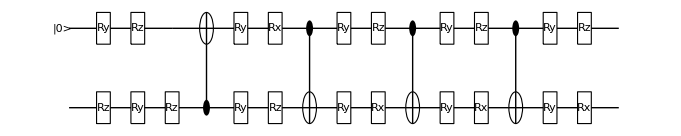

```mathematica
PrintCircuit[PickRandomCircuitIsometry[1,2,4]]
```

With TotGates->True this generates an isometry with the total number of gates, rather than the number of CNOTs

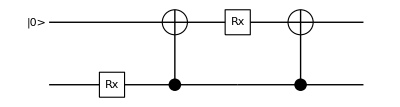

```mathematica
PrintCircuit[PickRandomCircuitIsometry[1,2,4,TotGates->True]]
```